```mathematica
(*Define the concentration span function M(t)*)M[t_]:=(1/2)-(1/2) Cos[(3*Pi/5)*t]

(*Find the time of maximum concentration span*)
maxTime=t/. FindMaximum[{M[t],0<=t<=6},t]

(*Calculate the 50-minute class period,50/60 hours*)
classDuration=50/60;
startTime=maxTime-classDuration/2;
endTime=maxTime+classDuration/2;

(*Plot the concentration span function M(t) over 6 hours,with class time highlighted*)
Plot[M[t],{t,0,6},GridLines->{{startTime,endTime},None},PlotLabel->"Concentration Span vs Time",AxesLabel->{"Time (hours after 9 AM)","Concentration Span"},PlotRange->{0,1},Epilog->{Red,Line[{{startTime,0},{startTime,1}}],Line[{{endTime,0},{endTime,1}}]}]

(*Calculate the minimum and maximum concentration span during the class period*)
classConcentration=Table[M[t],{t,startTime,endTime,0.01}];
MinMax[classConcentration]
```

ReplaceAll::rmix: Elements of {1.,{t→1.66667}} are a mixture of lists and nonlists.

t/.{1.,{t→1.66667}}

ReplaceAll::rmix: Elements of {1.,{t→1.66667}} are a mixture of lists and nonlists.

General::stop: Further output of ReplaceAll::rmix will be suppressed during this calculation.

-Graphics-

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of t/.{1.,{t→1.66667}}.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

{Hold[M[t]],Hold[M[t]]}

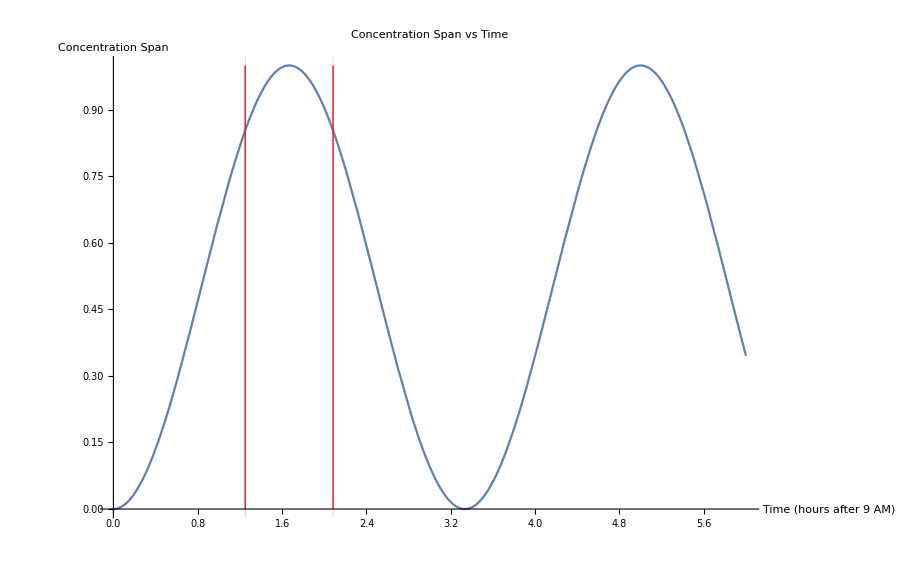

{0.853553,0.99999}

{1.,1.66667}

```mathematica
M[t_]:=(1/2)-(1/2) Cos[(3*Pi/5)*t]

(*Find the time of maximum concentration span*)
maxResult=FindMaximum[{M[t],0<=t<=6},t];
maxConcentration=maxResult[[1]];
maxTime=t/. maxResult[[2]];

(*Calculate the 50-minute class period,50/60 hours*)
classDuration=50/60;
startTime=maxTime-classDuration/2;
endTime=maxTime+classDuration/2;

(*Plot the concentration span function M(t) over 6 hours,with class time highlighted*)
Plot[M[t],{t,0,6},GridLines->{{startTime,endTime},None},PlotLabel->"Concentration Span vs Time",AxesLabel->{"Time (hours after 9 AM)","Concentration Span"},PlotRange->{0,1},Epilog->{Red,Line[{{startTime,0},{startTime,1}}],Line[{{endTime,0},{endTime,1}}]}]

classConcentration=Table[M[t],{t,startTime,endTime,0.01}];
MinMax[classConcentration]

{maxConcentration,maxTime}
```